FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Delta = 1. m, Beta = 90., Tensile strain demand = 0.00202935, Compressive strain demand = -0.00157666

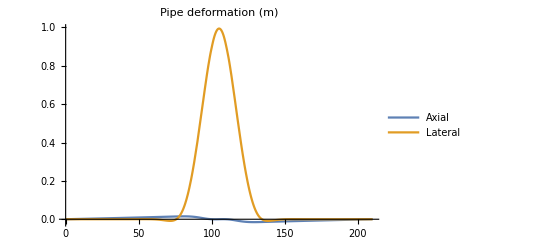

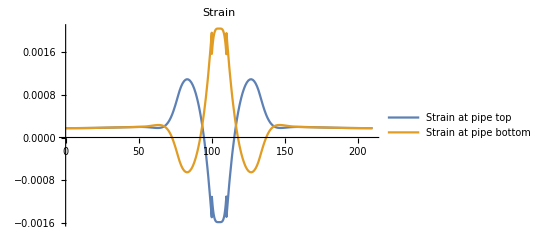

```mathematica
(*==========Program for material linearity==========*)
(****************************Module 1: Input parameters************************************)
Clear["Global`*"]
(*=====Geometric parameters=====*)
OD=457*10^-3;(*Outer diameter, m*)
WT=7.92*10^-3;(*Wall thickness, m*)
A=1/4*Pi*(OD^2-(OD-2*WT)^2);(*Section area, m^2*)
Inertia=Pi/64*(OD^4-(OD-2*WT)^4);(*Inertia, m^4*)

(*=====Pipe material parameters=====*)
Ee=1.99*10^11; (*Young's modulus, m*)
EeA=Ee*A;
EeI=Ee*Inertia;

(*=====Ground motion parameters=====*)
δ=1.0;(*Ground movement, m*)
β=90.Degree;(*Intersection angle, m*)
U=Chop[δ*Cos[β]];
W=Chop[δ*Sin[β]];

(*=====Length of each pipe segment, m=====*)
soilL=100;
soilM=10;
soilR=100;
L=soilL+soilM+soilR;

(*===== Soil spring properties =====*)
Tu=1.4*10^3;(*Axial soil spring resistance, N/m*)
tTu=5.*10^-3;
Pu=20.4*10^3;(*Lateral soil spring resistance, N/m*)
tPu=46*10^-3;
Qu=5.6*10^3;(*Uplift soil spring resistance, N/m*)
tQu=20.*10^-3;
Qd=55.*10^3;(*Bearing soil spring resistance, N/m*)
tQd=90.*10^-3;

choose=2;(*1 for symmetric soil force; 2 for non-symmetric force*)
axialSoilResis=Tu;
axialSoilDis=tTu;
lateralSoilResis=Pu;
lateralSoilDis=tPu;
lateralSoilResis1=Qu;
lateralSoilDis1=tQu;
lateralSoilResis2=Qd;
lateralSoilDis2=tQd;

(*********************Module 2: Calculations**********************************)
(* =====Node definition: vertical, horizontal, and soil===== *)
n1=n3=101.; (* Number of node *)
n2=41.;

n1=n1-1;
h1=soilL/n1;
ws1=Table[Symbol["ws1"<>ToString[i]],{i,0,n1}];
us1=Table[Symbol["us1"<>ToString[i]],{i,0,n1}];
xs1=Table[h1*i,{i,0,n1}];
Length[ws1];
ws1//MatrixForm;

n2=n2-1;
h2=soilM/n2;
ws2=Table[Symbol["ws2"<>ToString[i]],{i,0,n2}];
us2=Table[Symbol["us2"<>ToString[i]],{i,0,n2}];
xs2=Table[soilL+h2*i,{i,0,n2}];
Length[ws2];
ws2//MatrixForm;

n3=n3-1;
h3=soilR/n3;
ws3=Table[Symbol["ws3"<>ToString[i]],{i,0,n3}];
us3=Table[Symbol["us3"<>ToString[i]],{i,0,n3}];
xs3=Table[soilL+soilM+h3*i,{i,0,n3}];
Length[ws3];
ws3//MatrixForm;
xs=DeleteDuplicates[Join[xs1,xs2,xs3]];


blforceu1=Piecewise[{{axialSoilResis/axialSoilDis*u[x],-axialSoilDis≤u[x]≤axialSoilDis},{axialSoilResis,u[x]>axialSoilDis},{-axialSoilResis,u[x]<-axialSoilDis}},u[x]];
blforceu2=Piecewise[{{axialSoilResis/axialSoilDis*(U-u[x]),-axialSoilDis≤(U-u[x])≤axialSoilDis},{axialSoilResis,(U-u[x])>axialSoilDis},{-axialSoilResis,(U-u[x])<-axialSoilDis}},u[x]];
blforceu3=Piecewise[{{axialSoilResis/axialSoilDis*u[x],-axialSoilDis≤u[x]≤axialSoilDis},{axialSoilResis,u[x]>axialSoilDis},{-axialSoilResis,u[x]<-axialSoilDis}},u[x]];

Switch[choose,
1,
blforcew1=Piecewise[{{lateralSoilResis/lateralSoilDis*w[x],-lateralSoilDis≤w[x]≤lateralSoilDis},{lateralSoilResis,w[x]>lateralSoilDis},{-lateralSoilResis,w[x]<-lateralSoilDis}},w[x]];
blforcew2=Piecewise[{{lateralSoilResis/lateralSoilDis*(W-w[x]),-lateralSoilDis≤(W-w[x])≤lateralSoilDis},{lateralSoilResis,(W-w[x])>lateralSoilDis},{-lateralSoilResis,(W-w[x])<-lateralSoilDis}},w[x]];
blforcew3=Piecewise[{{lateralSoilResis/lateralSoilDis*w[x],-lateralSoilDis≤w[x]≤lateralSoilDis},{lateralSoilResis,w[x]>lateralSoilDis},{-lateralSoilResis,w[x]<-lateralSoilDis}},w[x]],
2,
blforcew1=Piecewise[{{lateralSoilResis1/lateralSoilDis1*w[x],-lateralSoilDis1≤w[x]≤lateralSoilDis1},{lateralSoilResis1,w[x]>lateralSoilDis1},{-lateralSoilResis1,w[x]<-lateralSoilDis1}},w[x]];
blforcew2=Piecewise[{{lateralSoilResis2/lateralSoilDis2*(W-w[x]),-lateralSoilDis2≤(W-w[x])≤lateralSoilDis2},{lateralSoilResis2,(W-w[x])>lateralSoilDis2},{-lateralSoilResis2,(W-w[x])<-lateralSoilDis2}},w[x]];
blforcew3=Piecewise[{{lateralSoilResis1/lateralSoilDis1*w[x],-lateralSoilDis1≤w[x]≤lateralSoilDis1},{lateralSoilResis1,w[x]>lateralSoilDis1},{-lateralSoilResis1,w[x]<-lateralSoilDis1}},w[x]]];

(*=====Pipe section 1=====*)
ws1p=Table[,{i,0,n1}];
ws1pp=Table[,{i,0,n1}];
ws1ppp=Table[,{i,0,n1}];
ws1pppp=Table[,{i,0,n1}];
us1p=Table[,{i,0,n1}];
us1pp=Table[,{i,0,n1}];
Do[us1p[[i]]=FullSimplify[(us1[[i+1]]-us1[[i-1]])/(xs1[[i+1]]-xs1[[i-1]])],{i,2,n1}];
us1p//MatrixForm;
Do[us1pp[[i]]=FullSimplify[(us1[[i+1]]-2us1[[i]]+us1[[i-1]])/h1^2],{i,2,n1}];
us1pp//MatrixForm;
Do[ws1p[[i]]=FullSimplify[(ws1[[i+1]]-ws1[[i-1]])/(xs1[[i+1]]-xs1[[i-1]])],{i,2,n1}];
ws1p//MatrixForm;
Do[ws1pp[[i]]=FullSimplify[(ws1[[i+1]]-2ws1[[i]]+ws1[[i-1]])/h1^2],{i,2,n1}];
ws1pp//MatrixForm;
Do[ws1ppp[[i]]=FullSimplify[(ws1[[i+2]]-2*ws1[[i+1]]+2ws1[[i-1]]-ws1[[i-2]])/2/h1^3],{i,3,n1-1}];
ws1ppp//MatrixForm;
Do[ws1pppp[[i]]=FullSimplify[(ws1[[i+2]]-4*ws1[[i+1]]+6ws1[[i]]-4ws1[[i-1]]+ws1[[i-2]])/h1^4],{i,3,n1-1}];
ws1pppp//MatrixForm;

(*=====Pipe section 2=====*)
ws2p=Table[,{i,0,n2}];
ws2pp=Table[,{i,0,n2}];
ws2ppp=Table[,{i,0,n2}];
ws2pppp=Table[,{i,0,n2}];
us2p=Table[,{i,0,n2}];
us2pp=Table[,{i,0,n2}];
Do[us2p[[i]]=FullSimplify[(us2[[i+1]]-us2[[i-1]])/(xs2[[i+1]]-xs2[[i-1]])],{i,2,n2}];
us2p//MatrixForm;
Do[us2pp[[i]]=FullSimplify[(us2[[i+1]]-2us2[[i]]+us2[[i-1]])/h2^2],{i,2,n2}];
us2pp//MatrixForm;
Do[ws2p[[i]]=FullSimplify[(ws2[[i+1]]-ws2[[i-1]])/(xs2[[i+1]]-xs2[[i-1]])],{i,2,n2}];
ws2p//MatrixForm;
Do[ws2pp[[i]]=FullSimplify[(ws2[[i+1]]-2ws2[[i]]+ws2[[i-1]])/h2^2],{i,2,n2}];
ws2pp//MatrixForm;
Do[ws2ppp[[i]]=FullSimplify[(ws2[[i+2]]-2*ws2[[i+1]]+2ws2[[i-1]]-ws2[[i-2]])/2/h2^3],{i,3,n2-1}];
ws2ppp//MatrixForm;
Do[ws2pppp[[i]]=FullSimplify[(ws2[[i+2]]-4*ws2[[i+1]]+6ws2[[i]]-4ws2[[i-1]]+ws2[[i-2]])/h2^4],{i,3,n2-1}];
ws2pppp//MatrixForm;

(*=====Pipe section 3=====*)
ws3p=Table[,{i,0,n3}];
ws3pp=Table[,{i,0,n3}];
ws3ppp=Table[,{i,0,n3}];
ws3pppp=Table[,{i,0,n3}];
us3p=Table[,{i,0,n3}];
us3pp=Table[,{i,0,n3}];
Do[us3p[[i]]=FullSimplify[(us3[[i+1]]-us3[[i-1]])/(xs3[[i+1]]-xs3[[i-1]])],{i,2,n3}];
us3p//MatrixForm;
Do[us3pp[[i]]=FullSimplify[(us3[[i+1]]-2us3[[i]]+us3[[i-1]])/h3^2],{i,2,n3}];
us3pp//MatrixForm;
Do[ws3p[[i]]=FullSimplify[(ws3[[i+1]]-ws3[[i-1]])/(xs3[[i+1]]-xs3[[i-1]])],{i,2,n3}];
ws2p//MatrixForm;
Do[ws3pp[[i]]=FullSimplify[(ws3[[i+1]]-2ws3[[i]]+ws3[[i-1]])/h3^2],{i,2,n3}];
ws3pp//MatrixForm;
Do[ws3ppp[[i]]=FullSimplify[(ws3[[i+2]]-2*ws3[[i+1]]+2ws3[[i-1]]-ws3[[i-2]])/2/h3^3],{i,3,n3-1}];
ws3ppp//MatrixForm;
Do[ws3pppp[[i]]=FullSimplify[(ws3[[i+2]]-4*ws3[[i+1]]+6ws3[[i]]-4ws3[[i-1]]+ws3[[i-2]])/h3^4],{i,3,n3-1}];
ws3pppp//MatrixForm;

(* Beam equation: Euler Bernoulli beam with large deflection  *)
Equations1=Table[EeA*(us1pp[[i]]+ws1p[[i]]*ws1pp[[i]])-(blforceu1/.u[x]->us1[[i]])==0,{i,2,n1}];
Equations1//MatrixForm;
Equations2=Table[EeI*ws1pppp[[i]]-EeA*(us1pp[[i]]+ws1p[[i]]*ws1pp[[i]])*ws1p[[i]]-EeA*(us1p[[i]]+1/2*ws1p[[i]]^2)*ws1pp[[i]]==-(blforcew1/.w[x]->ws1[[i]]),{i,3,n1-1}];
Equations2//MatrixForm;
Equations3=Table[EeA*(us2pp[[i]]+ws2p[[i]]*ws2pp[[i]])+(blforceu2/.u[x]->us2[[i]])==0,{i,2,n2}];
Equations3//MatrixForm;
Equations4=Table[EeI*ws2pppp[[i]]-EeA*(us2pp[[i]]+ws2p[[i]]*ws2pp[[i]])*ws2p[[i]]-EeA*(us2p[[i]]+1/2*ws2p[[i]]^2)*ws2pp[[i]]==(blforcew2/.w[x]->ws2[[i]]),{i,3,n2-1}];
Equations4//MatrixForm;
Equations5=Table[EeA*(us3pp[[i]]+ws3p[[i]]*ws3pp[[i]])-(blforceu3/.u[x]->us3[[i]])==0,{i,2,n3}];
Equations5//MatrixForm;
Equations6=Table[EeI*ws3pppp[[i]]-EeA*(us3pp[[i]]+ws3p[[i]]*ws3pp[[i]])*ws3p[[i]]-EeA*(us3p[[i]]+1/2*ws3p[[i]]^2)*ws3pp[[i]]==-(blforcew3/.w[x]->ws3[[i]]),{i,3,n3-1}];
Equations6//MatrixForm;

(*=====Boundary conditions=====*)
BCs=Table[,{i,1,18}];
(* Fix end: no displacement *)
BCs[[1]]=(us1[[1]]==0);
BCs[[2]]=(us3[[n3+1]]==0);
BCs[[3]]=(ws1[[1]]==0);
BCs[[4]]=(ws3[[n3+1]]==0);
(* Fix end: no rotation *)
BCs[[5]]=((ws1[[2]]-ws1[[1]])/(xs1[[2]]-xs1[[1]])==0);
BCs[[6]]=((ws3[[n3+1]]-ws3[[n3]])/(xs3[[n3+1]]-xs3[[n3]])==0);
(* The first connection *)
BCs[[7]]=(ws1[[n1+1]]==ws2[[1]]);
BCs[[8]]=((ws1[[n1+1]]-ws1[[n1]])/(xs1[[n1+1]]-xs1[[n1]])==(ws2[[2]]-ws2[[1]])/(xs2[[2]]-xs2[[1]]));
BCs[[9]]=((ws1[[n1+1]]-2ws1[[n1]]+ws1[[n1-1]])/(xs1[[n1+1]]-xs1[[n1]])^2==(ws2[[3]]-2ws2[[2]]+ws2[[1]])/(xs2[[2]]-xs2[[1]])^2);
BCs[[10]]=((ws1[[n1+1]]-3ws1[[n1]]+3ws1[[n1-1]]-ws1[[n1-2]])/(xs1[[n1+1]]-xs1[[n1]])^3==(ws2[[4]]-3ws2[[3]]+3ws2[[2]]-ws2[[1]])/(xs2[[2]]-xs2[[1]])^3);
BCs[[11]]=(us1[[n1+1]]==us2[[1]]);
BCs[[12]]=(us1[[n1+1]]-us1[[n1]])/(xs1[[n1+1]]-xs1[[n1]])==(us2[[2]]-us2[[1]])/(xs2[[2]]-xs2[[1]]);
(* The second connection *)
BCs[[13]]=(ws2[[n2+1]]==ws3[[1]]);
BCs[[14]]=((ws2[[n2+1]]-ws2[[n2]])/(xs2[[n2+1]]-xs2[[n2]])==(ws3[[2]]-ws3[[1]])/(xs3[[2]]-xs3[[1]]));
BCs[[15]]=((ws2[[n2+1]]-2ws2[[n2]]+ws2[[n2-1]])/(xs2[[n2+1]]-xs2[[n2]])^2==(ws3[[3]]-2ws3[[2]]+ws3[[1]])/(xs3[[2]]-xs3[[1]])^2);
BCs[[16]]=((ws2[[n2+1]]-3ws2[[n2]]+3ws2[[n2-1]]-ws2[[n2-2]])/(xs2[[n2+1]]-xs2[[n2]])^3==(ws3[[4]]-3ws3[[3]]+3ws3[[2]]-ws3[[1]])/(xs3[[2]]-xs3[[1]])^3);
BCs[[17]]=(us2[[n2+1]]==us3[[1]]);
BCs[[18]]=(us2[[n2+1]]-us2[[n2]])/(xs2[[n2+1]]-xs2[[n2]])==(us3[[2]]-us3[[1]])/(xs3[[2]]-xs3[[1]]);
BCs//MatrixForm;

(*=====Calculate unknowns=====*)
Equations=Flatten[{Equations1,Equations2,Equations3,Equations4,Equations5,Equations6,BCs}];
Unknowns=Flatten[{ws1,ws2,ws3,us1,us2,us3}];
Initvalues=Table[{Unknowns[[i]],1},{i,1,Length[Unknowns]}];
root=FindRoot[Equations,Initvalues];
us1data=Table[{xs1[[i]],(us1[[i]]/.root)},{i,1,Length[us1]}];
us2data=Table[{xs2[[i]],(us2[[i]]/.root)},{i,1,Length[us2]}];
us3data=Table[{xs3[[i]],(us3[[i]]/.root)},{i,1,Length[us3]}];
ws1data=Table[{xs1[[i]],(ws1[[i]]/.root)},{i,1,Length[ws1]}];
ws2data=Table[{xs2[[i]],(ws2[[i]]/.root)},{i,1,Length[ws2]}];
ws3data=Table[{xs3[[i]],(ws3[[i]]/.root)},{i,1,Length[ws3]}];

(*********************Module 3: Results**********************************)
(*====Deformation====*)
us1function=Interpolation[us1data,Method->"Spline",InterpolationOrder->3];
us2function=Interpolation[us2data,Method->"Spline",InterpolationOrder->3];
us3function=Interpolation[us3data,Method->"Spline",InterpolationOrder->3];
usfunction=Piecewise[{{us1function[x],0≤x<soilL},{us2function[x],soilL≤x<soilL+soilM},{us3function[x],soilL+soilM≤x≤L}}];
ws1function=Interpolation[ws1data,Method->"Spline",InterpolationOrder->3];
ws2function=Interpolation[ws2data,Method->"Spline",InterpolationOrder->3];
ws3function=Interpolation[ws3data,Method->"Spline",InterpolationOrder->3];
wsfunction=Piecewise[{{ws1function[x],0≤x<soilL},{ws2function[x],soilL≤x<soilL+soilM},{ws3function[x],soilL+soilM≤x≤L}}];

(*=====Strain calculation=====*)
strainTop=D[usfunction,x]+1/2*D[wsfunction,x]^2+D[wsfunction,{x,2}]*OD/2; (* Longitudinal strain along the pipe*)
strainBot=D[usfunction,x]+1/2*D[wsfunction,x]^2-D[wsfunction,{x,2}]*OD/2;
epsilonTop=Table[strainTop/.x->xs[[i]],{i,1,Length[xs]}];
epsilonBot=Table[strainBot/.x->xs[[i]],{i,1,Length[xs]}];
TSD=RankedMax[Join[epsilonTop,epsilonBot],choose];
CSD=RankedMin[Join[epsilonTop,epsilonBot],choose];
Print["Delta = ",δ," m",", Beta = ", β/Pi*180, ", Tensile strain demand = ", TSD, ", Compressive strain demand = ", CSD];

(*=====Visualization=====*)
deformation=Plot[{usfunction,wsfunction},{x,0,L},PlotRange->All,PlotLabel->"Pipe deformation (m)",PlotLegends->{"Axial","Lateral"}] (*Deformation*)
strain=Plot[{strainTop,strainBot},{x,0,L},PlotRange->All,PlotLabel->"Strain",PlotLegends->{"Strain at pipe top","Strain at pipe bottom"}](*Strain at extreme fibers*)
```